# 6planes.nb : the second-quantized Pin(4,4) spinor field dirac16complex, its 6-planes, gravity, Kohn-Sham pair creation and Einstein-Rosen bridges

This notebook is built on Patrick L. Nash's notebook Pre-gravity6plane.nb ((C) 2022, GNU General Public License) and mirrors its calculations for a NEW field, dirac16complex: a 16-component Pin(4,4) spinor field whose 16 complex components are anticommuting Grassmann variables (a second-quantized fermion field). Every matrix used below is defined exactly as in Pre-gravity6plane.nb and is checked entry-by-entry against that notebook's stored outputs (see the companion verification scripts in the repository).
The notebook is self-contained: evaluate it from top to bottom (Evaluation > Evaluate Notebook). All code is plain Wolfram Language; no external packages are loaded.
Reading guide for a beginning student: Part 1 builds the eight real 16x16 Dirac matrices (T16^A)[0..7]; Part 2 builds a tiny Grassmann-algebra engine; Part 3 defines dirac16complex and its Lagrangian; Part 4 mirrors the old notebook (field equations, couplings, exact solutions, light-like quanta, 7-planes and 6-planes); Parts 5-8 are the appended gravitational, Kohn-Sham (DFT) and Einstein-Rosen calculations.

## Part 0. Coordinates and conventions

The Cartesian coordinates of the project are X = {x0, x1, x2, x3, x4, x5, x6, x7}: x0 = hidden space, x1..x3 = 3-space, x4 = time, x5..x7 = superluminal ("deflating") time. The flat metric is eta4488 = diag(+1,+1,+1,+1,-1,-1,-1,-1), exactly as in Pre-gravity6plane.nb.

```mathematica
ClearAll["Global`*"];
X = {x0, x1, x2, x3, x4, x5, x6, x7};
eta4488 = ArrayFlatten[{{IdentityMatrix[4], 0}, {0, -IdentityMatrix[4]}}];
ID4 = IdentityMatrix[4]; ID8 = IdentityMatrix[8]; ID16 = IdentityMatrix[16];
Diagonal[eta4488]
```

{1,1,1,1,-1,-1,-1,-1}

## Part 1. The eight real 16x16 Dirac matrices (T16^A)[0..7]

### 1.1 Exact construction (identical to Pre-gravity6plane.nb)

Spinor metric sigma (8x8), self-dual (s4by4) and anti-self-dual (t4by4) 4x4 matrices, the six antisymmetric 8x8 matrices, tau[A], taubar[A] = sigma.Transpose[sigma.tau[A]], and finally (T16^A)[A] = [[0, taubar[A]], [tau[A], 0]]. In this notebook the symbol T16A[A] stands for (T16^A)[A] of Pre-gravity6plane.nb (the old notebook used the Notation package to make T16^A a symbol; here we use the plain name T16A to keep the notebook package-free).

```mathematica
sigma = ArrayFlatten[{{ConstantArray[0, {4, 4}], ID4}, {ID4, ConstantArray[0, {4, 4}]}}];
Qa[h_, p_, q_] := Signature[{h, p, q, 4}];
Qb[h_, p_, q_] := ID4[[p, 4]]*ID4[[q, h]] - ID4[[p, h]]*ID4[[q, 4]];
s4by4[h_] := Table[Qa[h, p, q] - Qb[h, p, q], {p, 4}, {q, 4}];   (* self-dual antisymmetric *)
t4by4[h_] := Table[Qa[h, p, q] + Qb[h, p, q], {p, 4}, {q, 4}];   (* anti-self-dual antisymmetric *)
sixAntiSymmetric8by8 = Flatten[{Table[ArrayFlatten[{{0, s4by4[h]}, {s4by4[h], 0}}], {h, 1, 3}],
    Table[ArrayFlatten[{{0, t4by4[h]}, {-t4by4[h], 0}}], {h, 3, 1, -1}]}, 1];
tau[0] = ID8; Do[tau[h] = sixAntiSymmetric8by8[[h]], {h, 1, 6}];
tau[7] = tau[1].tau[2].tau[3].tau[4].tau[5].tau[6];
Do[taubar[h] = sigma.Transpose[sigma.tau[h]], {h, 0, 7}];
Do[T16A[A] = ArrayFlatten[{{0, taubar[A]}, {tau[A], 0}}], {A, 0, 7}];
T16A[8] = Dot @@ Table[T16A[A], {A, 0, 7}];          (* chirality  Gamma = T0 T1 ... T7 *)
sigma16 = T16A[0].T16A[1].T16A[2].T16A[3];           (* spinor metric of dirac16complex *)
PL = (ID16 - T16A[8])/2; PR = (ID16 + T16A[8])/2;    (* chiral projectors *)
SAB = Table[(T16A[A].T16A[B] - T16A[B].T16A[A])/4, {A, 0, 7}, {B, 0, 7}];
Gamma5 = T16A[8];
MatrixForm /@ Table[T16A[A], {A, 0, 7}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

### 1.2 Proofs by exact computation

(a) every entry is a real integer; (b) {T_A, T_B} = 2 eta_AB I16 for all 64 pairs; (c) T_A is symmetric for A = 0..3 and antisymmetric for A = 4..7; (d) the chirality Gamma = T16A[8] = diag(-I8, I8) anticommutes with all eight; (e) P_L, P_R are complementary orthogonal projectors of rank 8; (f) sigma16 = diag(-sigma, sigma) is symmetric, squares to I16, has signature (8,8), and makes sigma16.T_A and sigma16.S_AB antisymmetric.

```mathematica
checksClifford = <|
  "real integer entries" -> And @@ Table[MatrixQ[T16A[A], IntegerQ], {A, 0, 7}],
  "{T_A,T_B} = 2 eta_AB I" -> And @@ Flatten@Table[T16A[A].T16A[B] + T16A[B].T16A[A] == 2 eta4488[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}],
  "T_A^T = eta_AA T_A" -> And @@ Table[Transpose[T16A[A]] == eta4488[[A + 1, A + 1]] T16A[A], {A, 0, 7}],
  "Gamma = diag(-I8,I8)" -> (Gamma5 == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]),
  "{Gamma,T_A} = 0" -> And @@ Table[Gamma5.T16A[A] + T16A[A].Gamma5 == 0 ID16, {A, 0, 7}],
  "Gamma^2 = I" -> (Gamma5.Gamma5 == ID16),
  "P_L, P_R projectors" -> (PL.PL == PL && PR.PR == PR && PL.PR == 0 ID16 && PL + PR == ID16 && MatrixRank[PL] == 8 == MatrixRank[PR]),
  "sigma16 = diag(-sigma,sigma)" -> (sigma16 == ArrayFlatten[{{-sigma, 0}, {0, sigma}}]),
  "sigma16 symmetric, sigma16^2 = I" -> (Transpose[sigma16] == sigma16 && sigma16.sigma16 == ID16),
  "signature of sigma16" -> Tally[Eigenvalues[sigma16]],
  "sigma16.T_A antisymmetric" -> And @@ Table[Transpose[sigma16.T16A[A]] == -sigma16.T16A[A], {A, 0, 7}],
  "sigma16.S_AB antisymmetric" -> And @@ Flatten@Table[Transpose[sigma16.SAB[[A, B]]] == -sigma16.SAB[[A, B]], {A, 8}, {B, 8}]|>
```

<|real integer entries→True,{T_A,T_B} = 2 eta_AB I→True,T_A^T = eta_AA T_A→True,Gamma = diag(-I8,I8)→True,{Gamma,T_A} = 0→True,Gamma^2 = I→True,P_L, P_R projectors→True,sigma16 = diag(-sigma,sigma)→True,sigma16 symmetric, sigma16^2 = I→True,signature of sigma16→{{-1,8},{1,8}},sigma16.T_A antisymmetric→True,sigma16.S_AB antisymmetric→True|>

### 1.3 The scaled commutators S_AB = (1/4)[T_A, T_B] generate Spin(4,4); with the reflections T_A they generate Pin(4,4)

We verify: (i) [S_AB, S_CD] = eta_BC S_AD - eta_AC S_BD - eta_BD S_AC + eta_AD S_BC (the so(4,4) relations); (ii) [S_AB, T_C] = eta_BC T_A - eta_AC T_B (vector action); (iii) the 28 matrices S_AB (A<B) are linearly independent; (iv) S_AB^2 = -(1/4) eta_AA eta_BB I16, so 12 generators are compact (rotations) and 16 non-compact (boosts); (v) g = exp(theta S_AB) acts on the vector index by a matrix Lambda(g) with Lambda^T eta Lambda = eta and det Lambda = 1; (vi) exp(2 Pi S_AB) = -I16 for compact generators (the 2-to-1 covering); (vii) the twisted adjoint action v -> -T_C v T_C^-1 is the reflection in the hyperplane orthogonal to e_C (det = -1). By the Cartan-Dieudonne theorem every element of O(4,4) is a product of at most 8 such reflections, hence the group generated by {exp(theta S_AB)} and {T_C} is Pin(4,4), the double cover of O(4,4).

```mathematica
etaE[A_, B_] := eta4488[[A + 1, B + 1]];
Sab[A_, B_] := SAB[[A + 1, B + 1]];
checkSO44 = And @@ Flatten@Table[Sab[A, B].Sab[C, D] - Sab[C, D].Sab[A, B] ==
      etaE[B, C] Sab[A, D] - etaE[A, C] Sab[B, D] - etaE[B, D] Sab[A, C] + etaE[A, D] Sab[B, C], {A, 0, 7}, {B, 0, 7}, {C, 0, 7}, {D, 0, 7}];
checkVector = And @@ Flatten@Table[Sab[A, B].T16A[C] - T16A[C].Sab[A, B] == etaE[B, C] T16A[A] - etaE[A, C] T16A[B], {A, 0, 7}, {B, 0, 7}, {C, 0, 7}];
gens = Flatten[Table[Sab[A, B], {A, 0, 6}, {B, A + 1, 7}], 1];
rank28 = MatrixRank[Flatten /@ gens];
squares = Union[Flatten[Table[Simplify[Sab[A, B].Sab[A, B] + (1/4) etaE[A, A] etaE[B, B] ID16 == 0 ID16], {A, 0, 6}, {B, A + 1, 7}]]];
compactCount = Count[Flatten[Table[etaE[A, A] etaE[B, B], {A, 0, 6}, {B, A + 1, 7}]], 1];
LambdaOf[g_] := Table[Tr[Inverse[g].T16A[C].g.T16A[D] etaE[D, D]]/16, {D, 0, 7}, {C, 0, 7}];  (* g^-1 T^C g = Lambda^C_D T^D *)
expS[A_, B_, th_] := MatrixExp[th Sab[A, B]];
checkLorentz = And @@ Flatten@Table[Module[{L = Simplify[LambdaOf[expS[A, B, th]], th \[Element] Reals]},
      {Simplify[Transpose[L].eta4488.L - eta4488] == 0 ID8, Simplify[Det[L]] == 1}], {A, 0, 6}, {B, A + 1, 7}];
check2Pi = Union[Flatten@Table[If[etaE[A, A] etaE[B, B] == 1, MatrixExp[2 Pi Sab[A, B]] == -ID16, True], {A, 0, 6}, {B, A + 1, 7}]];
reflection[C_] := Table[Tr[-T16A[C].T16A[D].Inverse[T16A[C]].T16A[E] etaE[E, E]]/16, {E, 0, 7}, {D, 0, 7}];
checkReflections = Table[{C, Det[reflection[C]], reflection[C] == eta4488.(ID8 - 2 Outer[Times, UnitVector[8, C + 1], UnitVector[8, C + 1]]).eta4488}, {C, 0, 7}];
<|"so(4,4) commutation relations" -> checkSO44, "[S_AB,T_C] = eta_BC T_A - eta_AC T_B" -> checkVector,
 "rank of the 28 S_AB" -> rank28, "S_AB^2 = -(1/4)eta_AA eta_BB I" -> squares, "compact generators" -> compactCount,
 "non-compact generators" -> 28 - compactCount, "Lambda(exp(theta S_AB)) in SO(4,4)" -> checkLorentz,
 "exp(2 Pi S_compact) = -I16" -> check2Pi, "reflections {C, det, equals diag reflection}" -> checkReflections|>
```

<|so(4,4) commutation relations→True,[S_AB,T_C] = eta_BC T_A - eta_AC T_B→True,rank of the 28 S_AB→28,S_AB^2 = -(1/4)eta_AA eta_BB I→{True},compact generators→12,non-compact generators→16,Lambda(exp(theta S_AB)) in SO(4,4)→True,exp(2 Pi S_compact) = -I16→{True},reflections {C, det, equals diag reflection}→{{0,-1,True},{1,-1,True},{2,-1,True},{3,-1,True},{4,-1,True},{5,-1,True},{6,-1,True},{7,-1,True}}|>

Example: a rotation in the (x1,x2)-plane (compact) and a boost in the (x0,x4)-plane (non-compact) in closed form:

```mathematica
{Simplify[expS[1, 2, th] - (Cos[th/2] ID16 + 2 Sin[th/2] Sab[1, 2])] == 0 ID16,
 Simplify[expS[0, 4, th] - (Cosh[th/2] ID16 + 2 Sinh[th/2] Sab[0, 4])] == 0 ID16}
```

{True,True}

### 1.4 The 256 products of the T's form a basis of all real 16x16 matrices (Cl(4,4) = M(16,R))

```mathematica
products = Table[Dot @@ (T16A /@ s), {s, Subsets[Range[0, 7], {1, 8}]}];
basis256 = Prepend[products, ID16];
{Length[basis256], MatrixRank[Flatten /@ basis256]}
```

{256,256}

## Part 2. A small exact Grassmann-algebra engine

dirac16complex has 16 complex components psi_a (a = 0..15) and their complex conjugates psi_a^*; these 32 objects (and their space-time derivatives) are anticommuting Grassmann generators: psi_a psi_b = - psi_b psi_a, in particular psi_a^2 = 0. An element of the Grassmann algebra is stored as an Association  <| {g1,...,gk} -> coefficient |>  with canonically ordered distinct generators. Complex conjugation reverses the order of factors, (theta eta)^* = eta^* theta^*, the standard convention compatible with Hermitian conjugation of field operators.

```mathematica
gClean[assoc_] := Select[DeleteCases[Map[Together, assoc], 0], True &];
gSortSign[list_] := Module[{ord = Ordering[list]}, If[Length[DeleteDuplicates[list]] < Length[list], {0, {}}, {Signature[ord], list[[ord]]}]];
gFromMono[c_, gens_List] := Module[{s = gSortSign[gens]}, If[s[[1]] == 0 || c === 0, <||>, <|s[[2]] -> s[[1]] c|>]];
gAdd[xs__Association] := gClean[Merge[{xs}, Total]];
gScale[c_, x_Association] := gClean[c # & /@ x];
gMul[x_Association, y_Association] := Module[{res = <||>},
  KeyValueMap[Function[{k1, c1}, KeyValueMap[Function[{k2, c2},
      Module[{s = gSortSign[Join[k1, k2]]}, If[s[[1]] =!= 0, res[s[[2]]] = Lookup[res, Key[s[[2]]], 0] + s[[1]] c1 c2]]], y]], x];
  gClean[res]];
gGen[g_] := <|{g} -> 1|>; gNum[c_] := If[c === 0, <||>, <|{} -> c|>];
gDL[g_, x_Association] := gClean[Association @@ KeyValueMap[Function[{k, c},
     With[{pos = FirstPosition[k, g, {0}][[1]]}, If[pos == 0, Nothing, Delete[k, pos] -> (-1)^(pos - 1) c]]], x]];   (* left derivative *)
gDR[g_, x_Association] := gClean[Association @@ KeyValueMap[Function[{k, c},
     With[{pos = FirstPosition[k, g, {0}][[1]]}, If[pos == 0, Nothing, Delete[k, pos] -> (-1)^(Length[k] - pos) c]]], x]];  (* right derivative *)
gDx[mu_, x_Association, Xs_List] := Module[{res = <||>},   (* total derivative d/dx_mu, Leibniz rule, order preserved *)
  KeyValueMap[Function[{k, c}, res = gAdd[res, gFromMono[D[c, Xs[[mu + 1]]], k]];
     Do[res = gAdd[res, gFromMono[c, ReplacePart[k, i -> (k[[i]] /. gen[t_, a_, d_] :> gen[t, a, Sort[Append[d, mu]]])]]], {i, Length[k]}]], x];
  gClean[res]];
gConjGen[gen[t_, a_, d_]] := gen[If[t === "psi", "psiS", "psi"], a, d];
gConj[x_Association, rule_ : {}] := Module[{res = <||>},
  KeyValueMap[Function[{k, c}, res = gAdd[res, gFromMono[Conjugate[c] /. rule, Reverse[gConjGen /@ k]]]], x]; gClean[res]];
psiF[d_ : {}] := Table[gGen[gen["psi", a, d]], {a, 0, 15}];
psiSF[d_ : {}] := Table[gGen[gen["psiS", a, d]], {a, 0, 15}];
gBil[u_List, M_, v_List] := Module[{res = <||>}, Do[If[M[[i, j]] =!= 0, res = gAdd[res, gScale[M[[i, j]], gMul[u[[i]], v[[j]]]]]], {i, Length[u]}, {j, Length[v]}]; res];
gMatVec[M_, v_List] := Table[Module[{res = <||>}, Do[If[M[[i, j]] =!= 0, res = gAdd[res, gScale[M[[i, j]], v[[j]]]]], {j, Length[v]}]; res], {i, Length[M]}];
gVecAdd[u_List, v_List] := MapThread[gAdd, {u, v}]; gVecScale[c_, u_List] := gScale[c, #] & /@ u;
gZeroQ[x_Association] := Length[gClean[x]] == 0;
gSimplify[x_Association, assum_ : True] := gClean[Simplify[#, assum] & /@ x];
gLinSub[x_Association, rule_] := Module[{res = <||>},
  KeyValueMap[Function[{k, c}, res = gAdd[res, gScale[c, If[k === {}, gNum[1], Fold[gMul, rule /@ k]]]]], x]; res];
p1 = gGen[gen["psi", 1, {}]]; p2 = gGen[gen["psi", 2, {}]]; s1 = gGen[gen["psiS", 1, {}]];
<|"psi1 psi2 + psi2 psi1 = 0" -> gZeroQ[gAdd[gMul[p1, p2], gMul[p2, p1]]], "psi1^2 = 0" -> gZeroQ[gMul[p1, p1]],
 "(psi1^* psi1)^* = psi1^* psi1" -> gZeroQ[gAdd[gConj[gMul[s1, p1]], gScale[-1, gMul[s1, p1]]]]|>
```

<|psi1 psi2 + psi2 psi1 = 0→True,psi1^2 = 0→True,(psi1^* psi1)^* = psi1^* psi1→True|>

## Part 3. The field dirac16complex and its Lagrangian

### 3.1 Definition

dirac16complex(x) = (psi_0(x), ..., psi_15(x)) is a 16-component Pin(4,4) spinor field on R^(4,4) with coordinates X. Each component is complex and Grassmann-odd: psi_a = (xi_a + I chi_a)/Sqrt[2] with xi_a, chi_a real Grassmann generators. Its Dirac adjoint is psibar = psi^dagger.sigma16 (the 16x16 version of the spinor metric of Pre-gravity6plane.nb). Under Spin(4,4), psi -> g psi with g = exp((1/2) omega^AB S_AB), and psibar psi is invariant because sigma16.S_AB is antisymmetric (Part 1).
dirac16complex is a SECOND-QUANTIZED field: the psi_a are operator-valued; the Grassmann variables used here are the classical (path-integral) counterparts of those operators. A c-number solution of the field equation (a "Universe", in the language of Pre-gravity6plane.nb) is a mode function of the field operator.

### 3.2 The Lagrangian: kinetic + mass (quadratic) + self-coupling (quartic)

L = (1/2) (psibar T^A d_A psi - (d_A psibar) T^A psi) - m psibar psi - (lam/2) (psibar psi)^2 .
The mass term is quadratic and the self-coupling quartic in the spinor components, in analogy with the Higgs potential mu^2 |phi|^2 + lambda |phi|^4 (the Higgs is a boson; here the field is a fermion, so (psibar psi)^2 is the lowest non-trivial self-coupling). Both terms are non-zero because the components are complex: for a real (Majorana) 16-component Grassmann field xi^T.sigma16.xi = 0 identically since sigma16 is symmetric.

```mathematica
psi = psiF[]; psiS = psiSF[]; dpsi[mu_] := psiF[{mu}]; dpsiS[mu_] := psiSF[{mu}];
Sbil = gBil[psiS, sigma16, psi];                                    (* psibar psi *)
kin1 = gAdd @@ Table[gBil[psiS, sigma16.T16A[A], dpsi[A]], {A, 0, 7}];   (* psibar T^A d_A psi *)
kin2 = gAdd @@ Table[gBil[dpsiS[A], sigma16.T16A[A], psi], {A, 0, 7}];   (* (d_A psibar) T^A psi *)
Lflat = gAdd[gScale[1/2, kin1], gScale[-1/2, kin2], gScale[-m, Sbil], gScale[-lam/2, gMul[Sbil, Sbil]]];
realRule = {Conjugate[m] -> m, Conjugate[lam] -> lam};
<|"number of Grassmann monomials in L" -> Length[Lflat], "mass term non-zero" -> (Length[Sbil] > 0), "quartic term non-zero" -> (Length[gMul[Sbil, Sbil]] > 0),
 "L is real: L^* - L = 0" -> gZeroQ[gAdd[gConj[Lflat, realRule], gScale[-1, Lflat]]]|>
```

<|number of Grassmann monomials in L→392,mass term non-zero→True,quartic term non-zero→True,L is real: L^* - L = 0→True|>

### 3.3 Euler-Lagrange equations (flat space), derived with Grassmann derivatives

Varying psi_a^* (left derivatives): dL/dpsi_a^* - d_mu ( dL/d(d_mu psi_a^*) ) = 0. We compare the 16 resulting Grassmann expressions with the matrix form sigma16.(T^A d_A psi - m psi - lam (psibar psi) psi).

```mathematica
ELflat = Table[gAdd[gDL[gen["psiS", a, {}], Lflat], gScale[-1, gAdd @@ Table[gDx[mu, gDL[gen["psiS", a, {mu}], Lflat], X], {mu, 0, 7}]]], {a, 0, 15}];
Tdpsi = Fold[gVecAdd, Table[gMatVec[T16A[A], dpsi[A]], {A, 0, 7}]];
expectedFlat = gMatVec[sigma16, gVecAdd[gVecAdd[Tdpsi, gVecScale[-m, psi]], gVecScale[-lam, Table[gMul[Sbil, psi[[b]]], {b, 16}]]]];
ELbFlat = Table[gAdd[gDR[gen["psi", a, {}], Lflat], gScale[-1, gAdd @@ Table[gDx[mu, gDR[gen["psi", a, {mu}], Lflat], X], {mu, 0, 7}]]], {a, 0, 15}];
<|"EL(psi^*) == sigma16.(T^A d_A psi - m psi - lam (psibar psi) psi)" -> And @@ MapThread[gZeroQ[gAdd[#1, gScale[-1, #2]]] &, {ELflat, expectedFlat}],
 "EL(psi) == complex conjugate of EL(psi^*)" -> And @@ MapThread[gZeroQ[gAdd[#1, gScale[-1, gConj[#2, realRule]]]] &, {ELbFlat, ELflat}]|>
```

<|EL(psi^*) == sigma16.(T^A d_A psi - m psi - lam (psibar psi) psi)→True,EL(psi) == complex conjugate of EL(psi^*)→True|>

Result (field equation of dirac16complex in flat space):  T^A d_A psi = (m + lam psibar psi) psi ,  A summed over 0..7 with T^A = T16A[A].  Example: the first component, written out:

```mathematica
showG[x_] := Total[KeyValueMap[#2 (Times @@ (#1 /. {gen["psi", a_, {}] :> Subscript[\[Psi], a], gen["psi", a_, {mu_}] :> Subscript["\[PartialD]", mu][Subscript[\[Psi], a]], gen["psiS", a_, {}] :> Subscript[\[Psi], a]^"*"})) &, x]];
showG[ELflat[[1]] /. lam -> 0]
```

m ψ_4-∂_0 [ψ_12]+∂_1 [ψ_11]-∂_2 [ψ_10]+∂_3 [ψ_9]-∂_4 [ψ_9]+∂_5 [ψ_10]+∂_6 [ψ_11]+∂_7 [ψ_12]

### 3.4 Noether current and its conservation

The U(1) symmetry psi -> Exp[I alpha] psi gives the conserved current J^A = psibar T^A psi. We verify d_A J^A = 0 when the field equations hold, by checking the algebraic identity d_A J^A = (EL-equation of psi) terms, i.e. d_A J^A = psibar.(T^A d_A psi) + (d_A psibar) T^A psi, and using the field equation T^A d_A psi = (m + lam S) psi together with its adjoint.

```mathematica
J = Table[gBil[psiS, sigma16.T16A[A], psi], {A, 0, 7}];
divJ = gAdd @@ Table[gDx[A, J[[A + 1]], X], {A, 0, 7}];
(* on-shell substitution: replace T^A d_A psi by (m + lam S) psi inside psibar(...) and its adjoint *)
onShell = gAdd[gBil[psiS, sigma16, Table[gAdd[gScale[m, psi[[b]]], gScale[lam, gMul[Sbil, psi[[b]]]]], {b, 16}]],
   gScale[-1, gConj[gBil[psiS, sigma16, Table[gAdd[gScale[m, psi[[b]]], gScale[lam, gMul[Sbil, psi[[b]]]]], {b, 16}]], realRule]]];
<|"d_A J^A = psibar(T.d psi) + (d psibar T)psi identity" -> gZeroQ[gAdd[divJ, gScale[-1, gAdd[kin1, kin2]]]],
 "on-shell value of d_A J^A" -> If[gZeroQ[onShell], 0, onShell]|>
```

<|d_A J^A = psibar(T.d psi) + (d psibar T)psi identity→True,on-shell value of d_A J^A→0|>

### 3.5 Second quantization: canonical anticommutators and the Krein form

Quantizing with x4 as time, the momentum conjugate to psi is pi = psibar T^4, and {psi_a(x), pi_b(y)} = I delta_ab delta(x-y) gives {psi_a, psi_b^dagger} = K_ab delta(x-y) with K = -I sigma16.T^4. K is Hermitian, K^2 = I16, with eight eigenvalues +1 and eight -1: the Fock space of dirac16complex carries an INDEFINITE (Krein) metric. This is unavoidable: the rotation by Pi in the (x4,x5)-plane, g45 = T16A[4].T16A[5] in Spin(4,4), maps K -> -K, so no Spin(4,4)-covariant positive charge density exists (with four time directions there is no invariant notion of 'positive time').

```mathematica
K = -I sigma16.T16A[4];
g45 = T16A[4].T16A[5];
alphaKS = -T16A[4].T16A[0]; betaKS = -I T16A[4];
<|"K Hermitian" -> (K == ConjugateTranspose[K]), "K^2 = I" -> (K.K == ID16), "eigenvalues of K" -> Tally[Eigenvalues[K]],
 "g45 = exp(Pi S_45) up to sign" -> (MatrixExp[Pi Sab[4, 5]] == g45 || MatrixExp[Pi Sab[4, 5]] == -g45),
 "g45^T.(sigma16 T^4).g45 = -(sigma16 T^4)" -> (Transpose[g45].sigma16.T16A[4].g45 == -sigma16.T16A[4]),
 "sigma16 = K.beta" -> (sigma16 == K.betaKS)|>
```

<|K Hermitian→True,K^2 = I→True,eigenvalues of K→{{-1,8},{1,8}},g45 = exp(Pi S_45) up to sign→True,g45^T.(sigma16 T^4).g45 = -(sigma16 T^4)→True,sigma16 = K.beta→True|>

### 3.6 The two mirror sectors: +mass and -mass universes

Since sigma16 = K.beta with beta = -I T^4, and K commutes with T^0, T^1, T^2, T^3, T^4 (but anticommutes with T^5, T^6, T^7), every field that does not depend on the superluminal times x5, x6, x7 splits as psi = psi_+ + psi_- with K psi_(+/-) = (+/-) psi_(+/-), and the Lagrangian splits EXACTLY into two copies with opposite overall sign:
L = L_D[psi_+] - L_D[psi_-] - (lam/2)(S_+ - S_-)^2 ,  L_D[chi] = chi^dagger beta (T^A d_A - m) chi (A = 0..4),  S_(+/-) = psi_(+/-)^dagger beta psi_(+/-).
So the 16-component field is a pair of 8-component universes whose energies (masses) enter with opposite signs. The quartic term couples them through -lam S_+ S_-.

```mathematica
<|"[K,T^A] = 0 for A=0..4" -> Table[K.T16A[A] == T16A[A].K, {A, 0, 4}], "{K,T^A} = 0 for A=5..7" -> Table[K.T16A[A] == -T16A[A].K, {A, 5, 7}],
 "Pplus.sigma16.T^A.Pminus = 0 (A=0..4): no cross terms" -> Table[(ID16 + K).sigma16.T16A[A].(ID16 - K) == 0 ID16, {A, 0, 4}],
 "Pplus.sigma16.Pplus == Pplus.beta.Pplus" -> ((ID16 + K).sigma16.(ID16 + K) == (ID16 + K).betaKS.(ID16 + K)),
 "Pminus.sigma16.Pminus == -Pminus.beta.Pminus" -> ((ID16 - K).sigma16.(ID16 - K) == -(ID16 - K).betaKS.(ID16 - K))|>
```

<|[K,T^A] = 0 for A=0..4→{True,True,True,True,True},{K,T^A} = 0 for A=5..7→{True,True,True},Pplus.sigma16.T^A.Pminus = 0 (A=0..4): no cross terms→{True,True,True,True,True},Pplus.sigma16.Pplus == Pplus.beta.Pplus→True,Pminus.sigma16.Pminus == -Pminus.beta.Pminus→True|>

## Part 4. Mirroring Pre-gravity6plane.nb: dirac16complex depending on x0 and x4

Pre-gravity6plane.nb studied Psi16 = f16[k][x0, x4], a 16-component wave function of a Universe that depends only on the hidden coordinate x0 and the time x4, with Lagrangian La = (1/H) Psi16^T.sigma16.Sum T^A d_A Psi16 + (2 M/H) Psi16^T.sigma16.Psi16. The corresponding configurations of dirac16complex are those that depend only on x0 and x4 (no dependence on x1, x2, x3, x5, x6, x7). For them the field equation is T^0 d0 psi + T^4 d4 psi = (m + lam psibar psi) psi. Comparing with the old notebook, whose field equation is T^A d_A Psi16 + 2 M Psi16 = 0, the old mass parameter corresponds to m = -2 M.

### 4.1 The Euler-Lagrange equations of dirac16complex depending on x0 and x4 (analogue of eLa)

```mathematica
Lx0x4 = gAdd[gScale[1/2, gAdd @@ Table[gBil[psiS, sigma16.T16A[A], dpsi[A]], {A, {0, 4}}]],
   gScale[-1/2, gAdd @@ Table[gBil[dpsiS[A], sigma16.T16A[A], psi], {A, {0, 4}}]], gScale[-m, Sbil], gScale[-lam/2, gMul[Sbil, Sbil]]];
eLax0x4 = Table[gAdd[gDL[gen["psiS", a, {}], Lx0x4], gScale[-1, gAdd @@ Table[gDx[mu, gDL[gen["psiS", a, {mu}], Lx0x4], X], {mu, {0, 4}}]]], {a, 0, 15}];
(* readable c-number form of the linear part (lam = 0):  rows of sigma16.(T^0 d0 + T^4 d4 - m) acting on f[k][x0,x4] *)
fvec = Table[f[k][x0, x4], {k, 0, 15}];
eLax0x4c = Simplify[sigma16.(T16A[0].D[fvec, x0] + T16A[4].D[fvec, x4] - m fvec)];
Column[eLax0x4c]
```

m f[4][x0,x4]-f[9]^(0,1)[x0,x4]-f[12]^(1,0)[x0,x4]
m f[5][x0,x4]+f[8]^(0,1)[x0,x4]-f[13]^(1,0)[x0,x4]
m f[6][x0,x4]+f[11]^(0,1)[x0,x4]-f[14]^(1,0)[x0,x4]
m f[7][x0,x4]-f[10]^(0,1)[x0,x4]-f[15]^(1,0)[x0,x4]
m f[0][x0,x4]+f[13]^(0,1)[x0,x4]-f[8]^(1,0)[x0,x4]
m f[1][x0,x4]-f[12]^(0,1)[x0,x4]-f[9]^(1,0)[x0,x4]
m f[2][x0,x4]-f[15]^(0,1)[x0,x4]-f[10]^(1,0)[x0,x4]
m f[3][x0,x4]+f[14]^(0,1)[x0,x4]-f[11]^(1,0)[x0,x4]
-m f[12][x0,x4]-f[1]^(0,1)[x0,x4]+f[4]^(1,0)[x0,x4]
-m f[13][x0,x4]+f[0]^(0,1)[x0,x4]+f[5]^(1,0)[x0,x4]
-m f[14][x0,x4]+f[3]^(0,1)[x0,x4]+f[6]^(1,0)[x0,x4]
-m f[15][x0,x4]-f[2]^(0,1)[x0,x4]+f[7]^(1,0)[x0,x4]
-m f[8][x0,x4]+f[5]^(0,1)[x0,x4]+f[0]^(1,0)[x0,x4]
-m f[9][x0,x4]-f[4]^(0,1)[x0,x4]+f[1]^(1,0)[x0,x4]
-m f[10][x0,x4]-f[7]^(0,1)[x0,x4]+f[2]^(1,0)[x0,x4]
-m f[11][x0,x4]+f[6]^(0,1)[x0,x4]+f[3]^(1,0)[x0,x4]

### 4.2 Which components are coupled (analogue of eLaCouplings)

```mathematica
coupledSets[eqs_] := Module[{raw = Table[Union[Cases[eqs[[j]], f[k_][__] :> k, Infinity], Cases[eqs[[j]], Derivative[__][f[k_]][__] :> k, Infinity]], {j, Length[eqs]}], g},
  g = Graph[Flatten[Table[UndirectedEdge @@@ Subsets[r, {2}], {r, raw}]]]; Sort[Sort /@ ConnectedComponents[g]]];
couplingsx0x4 = coupledSets[eLax0x4c]
```

{{0,5,8,13},{1,4,9,12},{2,7,10,15},{3,6,11,14}}

The coupling pattern {{0,5,8,13},{1,4,9,12},{2,7,10,15},{3,6,11,14}} is exactly the pattern eLaCouplings found in Pre-gravity6plane.nb: for configurations depending on x0 and x4, dirac16complex decomposes into four independent 4-component systems.

### 4.3 The variables z = 6 H x0, t = H x4 (analogue of eLazt) and the general exponential solution

With z = 6 H x0 and t = H x4 the linear equation becomes 6 T^0 d_z psi + T^4 d_t psi = (m/H) psi. A mode Exp[p z + q t] u solves it iff (6 p T^0 + q T^4 - m/H) u = 0, which is possible iff (6p)^2 - q^2 = (m/H)^2, i.e. (6p + q)(6p - q) = (m/H)^2. Writing 6p + q = 2C, the exponent is C (t + z/6) - (M^2/(C H^2)) (t - z/6) with m = -2M: this is EXACTLY the family of exponential solutions that Maple produced in Pre-gravity6plane.nb ('Solution 15feb'). Imaginary p, q give oscillatory plane waves (the generic case for a complex field).

```mathematica
modeLC[CC_, w_] := Module[{p = (CC + M^2/(CC H^2))/6, q = CC - M^2/(CC H^2)},
   (* solves 6 T^0 d_z psi + T^4 d_t psi + (2M/H) psi = 0  because (6pT0+qT4+2M/H)(6pT0+qT4-2M/H) = (36p^2-q^2-4M^2/H^2) I = 0 *)
   Exp[p z + q t] (6 p T16A[0] + q T16A[4] - 2 M/H ID16).w];
wGen = Table[1 + k, {k, 0, 15}];
solLC = modeLC[CC, wGen];
Simplify[6 T16A[0].D[solLC, z] + T16A[4].D[solLC, t] - (-2 M/H) solLC] == ConstantArray[0, 16]
```

True

```mathematica
(* oscillatory plane-wave mode of dirac16complex (depending on x0, x4) in the original coordinates:  psi = Exp[I (k x0 - En x4)] (I k T^0 - I En T^4 + m) w ,  En = +-Sqrt[k^2+m^2] *)
modeFunction[k_, mm_, w_, sgnE_ : 1] := With[{En = sgnE Sqrt[k^2 + mm^2]}, Exp[I (k x0 - En x4)] (I k T16A[0] - I En T16A[4] + mm ID16).w];
Table[Simplify[T16A[0].D[modeFunction[3/4, 1, wGen, s], x0] + T16A[4].D[modeFunction[3/4, 1, wGen, s], x4] - 1 modeFunction[3/4, 1, wGen, s]] == ConstantArray[0, 16], {s, {1, -1}}]
```

{True,True}

### 4.4 Retarded and advanced (light-cone) variables, and light-like quanta

As in Pre-gravity6plane.nb: ztadv = 6t + z, ztret = 6t - z (equivalently xiadv = x0 - x4, xiret = x0 + x4). For m = 0 the solutions depend on one light-cone variable only (e.g. on x0 - x4). For them every component of the U(1) current J^A = I psibar T^A psi and the scalar psibar psi vanish identically, because u = I k (T^0 - T^4) w with (T^0 - T^4)^2 = 0: exactly as the bilinears psi.sigma16.psi etc. vanished for the light-like quanta of Pre-gravity6plane.nb. These are the light-like quanta of dirac16complex.

```mathematica
lightLike = Exp[I kk (x0 - x4)] (I kk T16A[0] - I kk T16A[4]).wGen;      (* m = 0, depends only on x0 - x4 *)
scalarBil[ps_] := Simplify[Conjugate[ps].sigma16.ps, {kk, x0, x4} \[Element] Reals];
Jcur[ps_] := Table[Simplify[I Conjugate[ps].sigma16.T16A[A].ps, {kk, x0, x4} \[Element] Reals], {A, 0, 7}];
<|"solves the massless equation" -> (Simplify[T16A[0].D[lightLike, x0] + T16A[4].D[lightLike, x4]] == ConstantArray[0, 16]), "current J^A" -> Jcur[lightLike], "psibar psi" -> scalarBil[lightLike]|>
```

<|solves the massless equation→True,current J^A→{0,0,0,0,0,0,0,0},psibar psi→0|>

### 4.5 Triality frames and the vector forms of the type-1 and type-2 halves

Exactly as in Pre-gravity6plane.nb: the unit spinor is the 8th normalized eigenvector of sigma, unit = (1,0,0,0,1,0,0,0)/Sqrt[2]; the frames are F_A^a with columns eta_AA tau[A].unit and F_a^A with rows unit.sigma.taubar[A]; vectorFormOfType2 = F_a^A . psi2 and vectorFormOfType1 = eta4488.(psi1.sigma.F_A^a), where psi1 = components 0..7 (type 1) and psi2 = components 8..15 (type 2).

```mathematica
{evalues, evecs} = Eigensystem[sigma];
UU = ExpandAll[(1/Sqrt[2]) evecs]; unit = UU[[8]];
FAa = Transpose[Table[eta4488[[A + 1, A + 1]] (tau[A].unit), {A, 0, 7}]];
FaA = Table[unit.sigma.taubar[A], {A, 0, 7}];
vectorFormOfType2[psi2_] := FaA.psi2;
vectorFormOfType1[psi1_] := eta4488.(psi1.sigma.FAa);
{unit, unit.sigma.unit, FAa.FaA == ID8, FaA.FAa == ID8}
```

{{1/(√2),0,0,0,1/(√2),0,0,0},1,True,True}

### 4.6 7-planes and the 6-plane M6 created by dirac16complex

The field equation is REAL, so the real part Re psi of any dirac16complex mode depending on x0 and x4 is itself a real solution of the type studied in Pre-gravity6plane.nb. Applying the old notebook's construction to it: n1 = vectorFormOfType1[Re psi1] and n2 = vectorFormOfType2[Re psi2] are real 8-vectors depending on (x0, x4); 7-plane k = {Z in R^8 : n_k.Z = 0}; M6 = (7-plane 1) intersect (7-plane 2). For a real Psi16 this is literally the definition used in Pre-gravity6plane.nb. Generically all 28 = Binomial[8,2] coordinate pairs {z_i, z_j} can be solved for (the 28 parameterizations of M6).

```mathematica
psiU = modeFunction[3/4, 1, wGen, +1];
reU = ComplexExpand[Re[psiU]];
n1 = Simplify[vectorFormOfType1[reU[[1 ;; 8]]]]; n2 = Simplify[vectorFormOfType2[reU[[9 ;; 16]]]];
Zv = Array[z, 8];
minors[a_, b_] := Flatten[Table[Det[{{a[[i]], a[[j]]}, {b[[i]], b[[j]]}}], {i, 1, 7}, {j, i + 1, 8}]];
pt = {x0 -> 3/10, x4 -> 7/10};
M6sol = Solve[{(n1 /. pt).Zv == 0, (n2 /. pt).Zv == 0}, {z[7], z[8]}];
<|"Re psi solves the field equation" -> (Simplify[T16A[0].D[reU, x0] + T16A[4].D[reU, x4] - reU] == ConstantArray[0, 16]),
 "rank {n1,n2} at sample point" -> MatrixRank[N[{n1, n2} /. pt]], "valid parameterizations at sample point (of 28)" -> Count[N[minors[n1, n2] /. pt], x_ /; Abs[x] > 10^-12],
 "M6 at (x0,x4)=(3/10,7/10) solved for {z7,z8}" -> (M6sol /. (lhs_ -> rhs_) :> (lhs -> (Chop[Expand[N[rhs, 8]]] /. z[k_Real] :> z[Round[k]])))|>
```

<|Re psi solves the field equation→True,rank {n1,n2} at sample point→2,valid parameterizations at sample point (of 28)→28,M6 at (x0,x4)=(3/10,7/10) solved for {z7,z8}→{{z[7]→-132.8903 z[1]+189.9249 z[2]-174.9134 z[3]+155.9018 z[4]+77.04622 z[5]-74.04622 z[6],z[8]→-149.5254 z[1]+213.6894 z[2]-196.3014 z[3]+174.9134 z[4]+87.55199 z[5]-84.55199 z[6]}}|>

A pair of universes creates a 6-plane by itself: superpose a positive-energy and a negative-energy mode. Then Re V2 and Im V2 are independent and M6pair = {Z : Re V2.Z = 0, Im V2.Z = 0} is a 6-plane that moves with (x0, x4).

```mathematica
psiPair = modeFunction[3/4, 1, UnitVector[16, 1], +1] + modeFunction[3/4, 1, UnitVector[16, 10], -1];
W2 = Simplify[vectorFormOfType2[psiPair[[9 ;; 16]]]];
{r1, r2} = Simplify[ComplexExpand[{Re[W2], Im[W2]}], {x0, x4} \[Element] Reals];
<|"pair solves field equation" -> (Simplify[T16A[0].D[psiPair, x0] + T16A[4].D[psiPair, x4] - psiPair] == ConstantArray[0, 16]),
 "rank {Re V2, Im V2} at sample point" -> MatrixRank[N[{r1, r2} /. pt]]|>
```

<|pair solves field equation→True,rank {Re V2, Im V2} at sample point→2|>

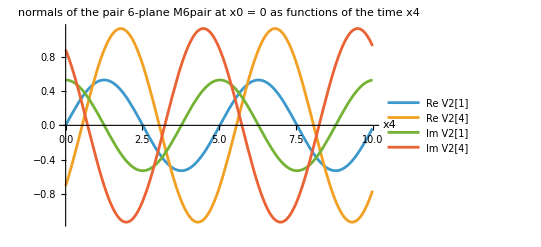

```mathematica
Plot[Evaluate[{r1[[1]], r1[[4]], r2[[1]], r2[[4]]} /. x0 -> 0], {x4, 0, 10}, PlotLegends -> {"Re V2[1]", "Re V2[4]", "Im V2[1]", "Im V2[4]"}, PlotLabel -> "normals of the pair 6-plane M6pair at x0 = 0 as functions of the time x4", AxesLabel -> {"x4", None}]
```

## Part 5 (appended). Euler-Lagrange equations of dirac16complex in the primordial, modern and future gravitational fields

A gravitational field is described by a co-frame (vielbein) e^A_mu, metric g_mu nu = eta_AB e^A_mu e^B_nu. We use diagonal vielbeins of the form found in Pre-gravity6plane.nb:
PRIMORDIAL field (exactly the vielbein of Pre-gravity6plane.nb with the inflationary choice a4[H x4] = H x4): e = diag( Tan[6 H x0], E^(-H x4) Sin[6 H x0]^(-1/6) (3 times), 1, E^(H x4) Sin[6 H x0]^(-1/6) (3 times) ), 0 < 6 H x0 < Pi/2.
MODERN field (static field of a mass along the hidden direction, Schwarzschild-type profile f = 1 - rs/x0): e = diag( f^(-1/2), 1, 1, 1, f^(1/2), 1, 1, 1 ), x0 > rs.
FUTURE field (mass plus dark energy, Schwarzschild-de Sitter-type profile f = 1 - rs/x0 - HL^2 x0^2): e = diag( f^(-1/2), 1, 1, 1, f^(1/2), 1, 1, 1 ), between the two horizons.
The covariant Lagrangian is L = Sqrt|g| [ (1/2)(psibar gamma^mu D_mu psi - (D_mu psibar) gamma^mu psi) - m psibar psi - (lam/2)(psibar psi)^2 ], gamma^mu = E_A^mu T^A, D_mu psi = d_mu psi + Omega_mu psi, D_mu psibar = d_mu psibar - psibar Omega_mu, Omega_mu = (1/4) omega_mu^A_B gamma_A gamma^B, omega_mu^A_B = e^A_nu (d_mu E_B^nu + Gamma^nu_{mu lambda} E_B^lambda). The sign of Omega is fixed by demanding covariant constancy of gamma^mu (checked below).

```mathematica
spinConnection[Evec_List, Xs_List] := Module[{e = DiagonalMatrix[Evec], Ei, g, gi, Gam, om, n = Length[Xs], Om, gam},
  Ei = Inverse[e]; g = Transpose[e].eta4488.e; gi = Inverse[g];
  Gam = Table[Simplify[(1/2) Sum[gi[[i, l]] (D[g[[l, j]], Xs[[k]]] + D[g[[l, k]], Xs[[j]]] - D[g[[j, k]], Xs[[l]]]), {l, n}]], {i, n}, {j, n}, {k, n}];
  om = Table[Simplify[Sum[e[[A, nu]] (D[Ei[[nu, B]], Xs[[mu]]] + Sum[Gam[[nu, mu, la]] Ei[[la, B]], {la, n}]), {nu, n}]], {mu, n}, {A, n}, {B, n}];
  Om = Table[Simplify[(1/4) Sum[om[[mu, A, B]] eta4488[[A, A]] T16A[A - 1].T16A[B - 1], {A, n}, {B, n}]], {mu, n}];
  gam = Table[Sum[Ei[[nu, A]] T16A[A - 1], {A, n}], {nu, n}];
  <|"Omega" -> Om, "Gamma" -> Gam, "gam" -> gam, "g" -> g|>];
covConst[sc_] := And @@ Flatten[Table[Simplify[D[sc["gam"][[nu]], X[[mu]]] + Sum[sc["Gamma"][[nu, mu, la]] sc["gam"][[la]], {la, 8}] + sc["Omega"][[mu]].sc["gam"][[nu]] - sc["gam"][[nu]].sc["Omega"][[mu]]] == 0 ID16, {mu, 8}, {nu, 8}]];
fM = 1 - rs/x0; fF = 1 - rs/x0 - HL^2 x0^2;
fields = <|
  "primordial" -> {Tan[6 H x0], E^(-H x4) Sin[6 H x0]^(-1/6), E^(-H x4) Sin[6 H x0]^(-1/6), E^(-H x4) Sin[6 H x0]^(-1/6), 1, E^(H x4) Sin[6 H x0]^(-1/6), E^(H x4) Sin[6 H x0]^(-1/6), E^(H x4) Sin[6 H x0]^(-1/6)},
  "modern" -> {fM^(-1/2), 1, 1, 1, fM^(1/2), 1, 1, 1},
  "future" -> {fF^(-1/2), 1, 1, 1, fF^(1/2), 1, 1, 1}|>;
realX = Element[{x0, x1, x2, x3, x4, x5, x6, x7}, Reals];
assum = <|"primordial" -> (H > 0 && 0 < x0 < Pi/(12 H) && realX), "modern" -> (rs > 0 && x0 > rs && realX), "future" -> (rs > 0 && HL > 0 && x0 > rs && fF > 0 && realX)|>;
realRuleG = {Conjugate[m] -> m, Conjugate[lam] -> lam, Conjugate[H] -> H, Conjugate[rs] -> rs, Conjugate[HL] -> HL, Conjugate[x0] -> x0, Conjugate[x4] -> x4};
gravityEL = <||>;
Do[Module[{sc = spinConnection[fields[c], X], Om, gam, sqrtg, k1, k2, s1, s2, L, EL, Dpsi, expected, spin},
   Om = sc["Omega"]; gam = sc["gam"];
   sqrtg = Simplify[Sqrt[Abs[Det[sc["g"]]]], assum[c]];
   k1 = gAdd @@ Table[gBil[psiS, sigma16.gam[[mu + 1]], dpsi[mu]], {mu, 0, 7}];
   k2 = gAdd @@ Table[gBil[dpsiS[mu], sigma16.gam[[mu + 1]], psi], {mu, 0, 7}];
   s1 = gBil[psiS, Simplify[sigma16.Sum[gam[[mu]].Om[[mu]], {mu, 8}]], psi];
   s2 = gBil[psiS, Simplify[sigma16.Sum[Om[[mu]].gam[[mu]], {mu, 8}]], psi];
   L = gScale[sqrtg, gAdd[gScale[1/2, k1], gScale[1/2, s1], gScale[-1/2, k2], gScale[1/2, s2], gScale[-m, Sbil], gScale[-lam/2, gMul[Sbil, Sbil]]]];
   EL = Table[gSimplify[gAdd[gDL[gen["psiS", a, {}], L], gScale[-1, gAdd @@ Table[gDx[mu, gDL[gen["psiS", a, {mu}], L], X], {mu, 0, 7}]]], assum[c]], {a, 0, 15}];
   Dpsi = Fold[gVecAdd, Table[gMatVec[gam[[mu + 1]], gVecAdd[dpsi[mu], gMatVec[Om[[mu + 1]], psi]]], {mu, 0, 7}]];
   expected = gMatVec[sqrtg sigma16, gVecAdd[gVecAdd[Dpsi, gVecScale[-m, psi]], gVecScale[-lam, Table[gMul[Sbil, psi[[b]]], {b, 16}]]]];
   spin = Simplify[Sum[gam[[mu]].Om[[mu]], {mu, 8}], assum[c]];
   gravityEL[c] = <|"covariantly constant gamma^mu" -> covConst[sc], "Sqrt|g|" -> sqrtg,
     "L real" -> gZeroQ[gSimplify[gAdd[gConj[L, realRuleG], gScale[-1, L]], assum[c]]],
     "EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam S psi)" -> (And @@ MapThread[gZeroQ[gSimplify[gAdd[#1, gScale[-1, #2]], assum[c]]] &, {EL, expected}]),
     "gamma^mu Omega_mu (coefficient of T^0; all other T^A coefficients vanish)" -> {Simplify[Tr[spin.T16A[0]]/16, assum[c]], Table[Simplify[Tr[spin.T16A[A]], assum[c]], {A, 1, 7}]},
     "gamma^mu (E_A^mu factors)" -> Table[Simplify[1/fields[c][[A + 1]], assum[c]], {A, 0, 7}]|>], {c, Keys[fields]}];
gravityEL
```

<|primordial→<|covariantly constant gamma^mu→True,Sqrt|g|→Sec[6 H x0],L real→True,EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam S psi)→True,gamma^mu Omega_mu (coefficient of T^0; all other T^A coefficients vanish)→{-3 H Cot[6 H x0]^2,{0,0,0,0,0,0,0}},gamma^mu (E_A^mu factors)→{Cot[6 H x0],ⅇ^(H x4) Sin[6 H x0]^(1/6),ⅇ^(H x4) Sin[6 H x0]^(1/6),ⅇ^(H x4) Sin[6 H x0]^(1/6),1,ⅇ^(-H x4) Sin[6 H x0]^(1/6),ⅇ^(-H x4) Sin[6 H x0]^(1/6),ⅇ^(-H x4) Sin[6 H x0]^(1/6)}|>,modern→<|covariantly constant gamma^mu→True,Sqrt|g|→1,L real→True,EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam S psi)→True,gamma^mu Omega_mu (coefficient of T^0; all other T^A coefficients vanish)→{rs/(4 √(x0^3 (-rs+x0))),{0,0,0,0,0,0,0}},gamma^mu (E_A^mu factors)→{√(1-rs/x0),1,1,1,1/(√(1-rs/x0)),1,1,1}|>,future→<|covariantly constant gamma^mu→True,Sqrt|g|→1,L real→True,EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam S psi)→True,gamma^mu Omega_mu (coefficient of T^0; all other T^A coefficients vanish)→{(rs-2 HL^2 x0^3)/(4 √(-x0^3 (rs-x0+HL^2 x0^3))),{0,0,0,0,0,0,0}},gamma^mu (E_A^mu factors)→{√(1-rs/x0-HL^2 x0^2),1,1,1,1/(√(1-rs/x0-HL^2 x0^2)),1,1,1}|>|>

Hence the Euler-Lagrange equations of dirac16complex in the three gravitational fields are, explicitly (A summed over 0..7, T^A = T16A[A]):
PRIMORDIAL:  Cot[6Hx0] T^0 d0 psi + E^(H x4) Sin[6Hx0]^(1/6) (T^1 d1 + T^2 d2 + T^3 d3) psi + T^4 d4 psi + E^(-H x4) Sin[6Hx0]^(1/6) (T^5 d5 + T^6 d6 + T^7 d7) psi - 3 H Cot[6Hx0]^2 T^0 psi = (m + lam psibar psi) psi .
MODERN:      Sqrt[f] T^0 d0 psi + (T^1 d1 + T^2 d2 + T^3 d3) psi + f^(-1/2) T^4 d4 psi + (T^5 d5 + T^6 d6 + T^7 d7) psi + (f'/(4 Sqrt[f])) T^0 psi = (m + lam psibar psi) psi , f = 1 - rs/x0 .
FUTURE:      the same as MODERN with f = 1 - rs/x0 - HL^2 x0^2 .
For configurations depending only on x0 and x4, only the T^0 and T^4 terms survive.

### 5.1 Mass-sign pairing holds in every gravitational field

Two maps send the Lagrangian with mass +m to the Lagrangian with mass -m, in each field: (a) the antilinear 'charge conjugation' C: psi -> Gamma psi^* (Gamma = T16A[8]); (b) the Pin(4,4) reflection P1: psi(x) -> T16A[1] psi(R1 x), R1: x1 -> -x1 (an isometry of all three fields). We verify L_(m,lam)[C psi] = L_(-m,lam)[psi] and L_(m,lam)[P1 psi] = L_(-m,lam)[psi] as exact identities in the Grassmann algebra.

```mathematica
pairingChecks = <||>;
Do[Module[{sc = spinConnection[fields[c], X], Om, gam, sqrtg, L, ruleC, ruleP},
   Om = sc["Omega"]; gam = sc["gam"]; sqrtg = Simplify[Sqrt[Abs[Det[sc["g"]]]], assum[c]];
   L = gScale[sqrtg, gAdd[gScale[1/2, gAdd @@ Table[gBil[psiS, sigma16.gam[[mu + 1]], dpsi[mu]], {mu, 0, 7}]], gScale[1/2, gBil[psiS, Simplify[sigma16.Sum[gam[[mu]].Om[[mu]], {mu, 8}]], psi]],
      gScale[-1/2, gAdd @@ Table[gBil[dpsiS[mu], sigma16.gam[[mu + 1]], psi], {mu, 0, 7}]], gScale[1/2, gBil[psiS, Simplify[sigma16.Sum[Om[[mu]].gam[[mu]], {mu, 8}]], psi]], gScale[-m, Sbil], gScale[-lam/2, gMul[Sbil, Sbil]]]];
   ruleC[gen["psi", a_, d_]] := gAdd @@ Table[gScale[Gamma5[[a + 1, b + 1]], gGen[gen["psiS", b, d]]], {b, 0, 15}];
   ruleC[gen["psiS", a_, d_]] := gAdd @@ Table[gScale[Gamma5[[a + 1, b + 1]], gGen[gen["psi", b, d]]], {b, 0, 15}];
   ruleP[gen[t_, a_, d_]] := gScale[(-1)^Count[d, 1], gAdd @@ Table[gScale[T16A[1][[a + 1, b + 1]], gGen[gen[t, b, d]]], {b, 0, 15}]];
   pairingChecks[c] = <|"L[Gamma psi^*] == L(m->-m)[psi]" -> gZeroQ[gSimplify[gAdd[gLinSub[L, ruleC], gScale[-1, L /. m -> -m]], assum[c]]],
     "L[T1 psi(R1x)] == L(m->-m)[psi](R1x)" -> gZeroQ[gSimplify[gAdd[gLinSub[L, ruleP], gScale[-1, L /. m -> -m]], assum[c]]]|>], {c, Keys[fields]}];
pairingChecks
```

<|primordial→<|L[Gamma psi^*] == L(m->-m)[psi]→True,L[T1 psi(R1x)] == L(m->-m)[psi](R1x)→True|>,modern→<|L[Gamma psi^*] == L(m->-m)[psi]→True,L[T1 psi(R1x)] == L(m->-m)[psi](R1x)→True|>,future→<|L[Gamma psi^*] == L(m->-m)[psi]→True,L[T1 psi(R1x)] == L(m->-m)[psi](R1x)→True|>|>

## Part 6 (appended). DFT-motivated Kohn-Sham approximation: ground and first excited states

### 6.1 The Kohn-Sham equation of dirac16complex in a static gravitational field

For a static field with lapse B(x0) = e^4_4 and hidden scale N(x0) = e^0_0, a stationary mode psi = Exp[-I eps x4] u(x0) of the field equation, after the rescaling u -> (Sqrt|g|/N)^(1/2) u (which removes the spin-connection term) and in the tortoise coordinate rho with d rho = (N/B) dx0, obeys the Kohn-Sham equation
h_KS chi = eps chi ,  h_KS = alpha p + W(rho) beta ,  p = -I d/d rho ,  alpha = -T^4 T^0 ,  beta = -I T^4 ,  W = B (m + lam rho_s) .
The quartic self-coupling is treated in the Kohn-Sham (Hartree, scalar-channel) approximation: (lam/2)(psibar psi)^2 -> lam rho_s psibar psi - (lam/2) rho_s^2 with rho_s = <psibar psi> computed from the occupied Kohn-Sham orbitals (a local, LDA-type density functional). alpha and beta are Hermitian anticommuting involutions that commute with K, so h_KS is 8 copies (4 with K = +1, 4 with K = -1) of the 2x2 operator [[0, A^T],[A, 0]], A = d/d rho + W. Bag boundary conditions u(rho_L) = 0, v(rho_R) = 0 are imposed. Its spectrum is EXACTLY symmetric, eps <-> -eps: the unitary T^0 and the antiunitary complex conjugation both anticommute with h_KS.

```mathematica
<|"alpha, beta Hermitian involutions, anticommuting" -> {alphaKS == ConjugateTranspose[alphaKS], betaKS == ConjugateTranspose[betaKS], alphaKS.alphaKS == ID16, betaKS.betaKS == ID16, alphaKS.betaKS + betaKS.alphaKS == 0 ID16},
 "[K,alpha] = [K,beta] = [K,T^0] = 0" -> {K.alphaKS == alphaKS.K, K.betaKS == betaKS.K, K.T16A[0] == T16A[0].K},
 "T^0 alpha T^0 = -alpha, T^0 beta T^0 = -beta (unitary pairing)" -> {T16A[0].alphaKS.T16A[0] == -alphaKS, T16A[0].betaKS.T16A[0] == -betaKS},
 "alpha real, beta imaginary (antiunitary pairing h^* = -h)" -> {Conjugate[alphaKS] == alphaKS, Conjugate[betaKS] == -betaKS},
 "bag operator T^0 = -I alpha.beta" -> (T16A[0] == -I alphaKS.betaKS)|>
```

<|alpha, beta Hermitian involutions, anticommuting→{True,True,True,True,True},[K,alpha] = [K,beta] = [K,T^0] = 0→{True,True,True},T^0 alpha T^0 = -alpha, T^0 beta T^0 = -beta (unitary pairing)→{True,True},alpha real, beta imaginary (antiunitary pairing h^* = -h)→{True,True},bag operator T^0 = -I alpha.beta→True|>

### 6.2 Numerical Kohn-Sham solver (staggered grid, exact eps <-> -eps symmetry)

```mathematica
ksMatrixA[Whalf_List, d_] := Module[{n = Length[Whalf]},
  SparseArray[Join[Table[{j, j} -> 1/d + Whalf[[j]]/2, {j, 1, n}], Table[{j, j - 1} -> -1/d + Whalf[[j]]/2, {j, 2, n}]], {n, n}]];
ksSolveW[Wh_List, d_] := Module[{A = Normal[ksMatrixA[Wh, d]], P, S, Q, s, ord},
  {P, S, Q} = SingularValueDecomposition[N[A]]; s = Diagonal[S]; ord = Ordering[s];
  <|"s" -> s[[ord]], "Q" -> Q[[All, ord]], "P" -> P[[All, ord]], "d" -> d|>];
ksScalarDensity[sol_, k_] := Module[{q = sol["Q"][[All, k]], p = sol["P"][[All, k]], d = sol["d"], qh}, qh = (q + Prepend[Most[q], 0])/2; 2 qh p/(2 d)];
(* test against the analytic bag spectrum  k Cos[k L] + m Sin[k L] = 0 , eps = Sqrt[k^2 + m^2] *)
Module[{sol = ksSolveW[ConstantArray[1., 1600], 5./1600], ks},
 ks = k /. Table[FindRoot[k Cos[5 k] + Sin[5 k] == 0, {k, k0}], {k0, {0.6, 1.2, 1.9}}];
 <|"numerical levels" -> Take[sol["s"], 3], "analytic levels" -> Sqrt[ks^2 + 1]|>]
```

<|numerical levels→{1.13204,1.47963,1.95318},analytic levels→{1.13211,1.47986,1.95361}|>

### 6.3 Self-consistent field, two vacua, ground and first excited states

Each of the 8 copies contributes to rho_s. Because sigma16 = K.beta, the K = -1 copies enter psibar psi with a minus sign. Two natural vacua exist. V1 (Spin(4,4)-symmetric vacuum, zeta = +1): both sectors fill their negative-field-energy levels; the two condensates ADD, rho_s = 8 rho_copy, and a dynamical mass is generated self-consistently (as in the Nambu-Jona-Lasinio model; the grid spacing is the ultraviolet cutoff). V2 (zero-energy mirror vacuum, zeta = -1): both sectors fill eps < 0; the condensates CANCEL, rho_s = 0, W = B m exactly, and the total vacuum energy is exactly 0. The first excited state is computed by Delta-SCF: one particle-hole pair in the lowest level of one copy, with the field re-solved self-consistently.

```mathematica
dftSCF[Bv_List, d_, mm_, lm_, zeta_, excite_ : 0, T_ : 0, mix_ : 0.5, tol_ : 1.*^-11, maxit_ : 500] :=
 Module[{M = ConstantArray[N[mm], Length[Bv]], sol, dens, w, rhoCopy, rhos, Mnew, it = 0, err = 1., s, Eband, Eint},
  While[err > tol && it < maxit, it++;
   sol = ksSolveW[Bv M, d]; s = sol["s"]; dens = Table[ksScalarDensity[sol, k], {k, Length[s]}];
   w = If[T == 0, ConstantArray[1., Length[s]], Tanh[s/(2 T)]];
   rhoCopy = -w.dens; rhos = 4 rhoCopy + zeta 4 rhoCopy + Total[excite] 2 dens[[1]];
   Mnew = mm + lm rhos; err = Max[Abs[Mnew - M]]; M = (1 - mix) M + mix Mnew];
  sol = ksSolveW[Bv M, d]; s = sol["s"];
  Eband = If[T == 0, -4 Total[s] - 4 zeta Total[s] + Total[2 s[[1]] excite],
    4 Total[-s - 2 T Log[1 + Exp[-s/T]]] + zeta 4 Total[-s - 2 T Log[1 + Exp[-s/T]]]];
  Eint = -(lm/2) Total[Bv rhos^2] d;
  <|"M" -> M, "s" -> s, "iterations" -> it, "E" -> Eband + Eint, "Eband" -> Eband, "Eint" -> Eint|>];
Hn = 1.; rsn = 1.; HLn = 0.1; mn = 1.; lamn = -0.03; dgrid = 0.02;
fFn[x_] := 1 - rsn/x - HLn^2 x^2;
horizonsF = Sort[x /. NSolve[x fFn[x] == 0 && x > 0, x, Reals]];
tortF = Interpolation[Table[{NIntegrate[1/fFn[y], {y, 3., x}], x}, {x, Subdivide[horizonsF[[1]] + 0.002, horizonsF[[2]] - 0.002, 4000]}]];
maps = <|"primordial" -> {ArcCos[Exp[-6 Hn #]]/(6 Hn) &, 1. &, {0., 4.}},
   "modern" -> {rsn (1 + ProductLog[Exp[#/rsn - 1]]) &, Sqrt[1 - rsn/#] &, {-4., 6.}},
   "future" -> {tortF[#] &, Sqrt[fFn[#]] &, {-3., 3.}}|>;
dftResults = <||>;
Do[Module[{xmap, Bfun, rL, rR, n, d, rv, Bv, v2, v2p, v2m, v2pair, v1, v1x},
   {xmap, Bfun, {rL, rR}} = maps[c]; n = Round[(rR - rL)/dgrid]; d = (rR - rL)/n;
   rv = Table[rL + (j - 1/2) d, {j, n}]; Bv = Bfun /@ (xmap /@ rv);
   v2 = dftSCF[Bv, d, mn, lamn, -1]; v2p = dftSCF[Bv, d, mn, lamn, -1, {+1}]; v2m = dftSCF[Bv, d, mn, lamn, -1, {-1}]; v2pair = dftSCF[Bv, d, mn, lamn, -1, {+1, -1}];
   v1 = dftSCF[Bv, d, mn, lamn, +1]; v1x = dftSCF[Bv, d, mn, lamn, +1, {+1}];
   dftResults[c] = <|"rho grid" -> rv, "B" -> Bv, "x0 range" -> MinMax[xmap /@ rv],
     "V2: max|W/B - m|" -> Max[Abs[v2["M"] - mn]], "V2: E_vacuum" -> v2["E"], "V2: lowest levels" -> Take[v2["s"], 3],
     "V2: dE(+ universe pair)" -> v2p["E"] - v2["E"], "V2: dE(- universe pair)" -> v2m["E"] - v2["E"], "V2: dE(both, created together)" -> v2pair["E"] - v2["E"],
     "V1: M range" -> MinMax[v1["M"]], "V1: E0" -> v1["E"], "V1: E1-E0 (Delta-SCF)" -> v1x["E"] - v1["E"], "V1: lowest levels" -> Take[v1["s"], 3],
     "V1: M profile" -> v1["M"], "V1 iterations" -> v1["iterations"]|>], {c, Keys[maps]}];
KeyDrop[#, {"rho grid", "B", "V1: M profile"}] & /@ dftResults
```

<|primordial→<|x0 range→{0.0571594,0.261799},V2: max|W/B - m|→0.,V2: E_vacuum→0.,V2: lowest levels→{1.18792,1.66827,2.29936},V2: dE(+ universe pair)→2.35992,V2: dE(- universe pair)→-2.39177,V2: dE(both, created together)→0.,V1: M range→{1.53525,6.23306},V1: E0→-101780.,V1: E1-E0 (Delta-SCF)→3.33886,V1: lowest levels→{1.6818,2.07587,2.62805},V1 iterations→55|>,modern→<|x0 range→{1.00676,4.68557},V2: max|W/B - m|→0.,V2: E_vacuum→0.,V2: lowest levels→{0.478383,0.833191,1.04954},V2: dE(+ universe pair)→0.95461,V2: dE(- universe pair)→-0.958925,V2: dE(both, created together)→0.,V1: M range→{1.10022,6.10464},V1: E0→-254548.,V1: E1-E0 (Delta-SCF)→1.03858,V1: lowest levels→{0.520477,0.971297,1.24416},V1 iterations→53|>,future→<|x0 range→{1.55993,4.74802},V2: max|W/B - m|→0.,V2: E_vacuum→0.,V2: lowest levels→{0.859668,1.15294,1.56262},V2: dE(+ universe pair)→1.7113,V2: dE(- universe pair)→-1.72737,V2: dE(both, created together)→0.,V1: M range→{1.34987,6.17439},V1: E0→-152692.,V1: E1-E0 (Delta-SCF)→2.23828,V1: lowest levels→{1.12479,1.37113,1.7368},V1 iterations→51|>|>

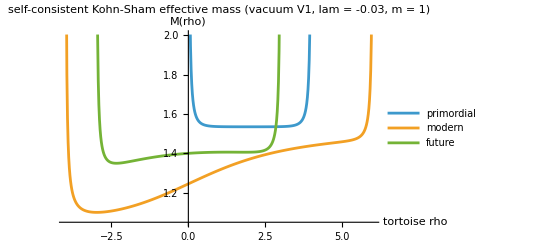

```mathematica
ListLinePlot[Table[Transpose[{dftResults[c]["rho grid"], dftResults[c]["V1: M profile"]}], {c, Keys[maps]}], PlotLegends -> Keys[maps],
 AxesLabel -> {"tortoise rho", "M(rho)"}, PlotLabel -> "self-consistent Kohn-Sham effective mass (vacuum V1, lam = -0.03, m = 1)"]
```

### 6.4 Kohn-Sham fermion-gas thermodynamic effective potential Omega(T)

Mermin-Kohn-Sham grand potential at temperature T (chemical potential 0) for vacuum V1: Omega = 8 Sum_k ( -s_k - 2 T Log[1 + Exp[-s_k/T]] ) - (lam/2) Integral B rho_s^2 d rho, with rho_s = -Sum_k Tanh[s_k/(2T)] (density of level k), solved self-consistently at each T. The Hawking temperatures of the bridges of Part 8 are T_H = f'(x_h)/(4 Pi): modern T_H = 1/(4 Pi rs).

```mathematica
THmodern = 1/(4 Pi rsn);
thermo = Table[Module[{xmap, Bfun, rL, rR, n, d, rv, Bv},
    {xmap, Bfun, {rL, rR}} = maps[c]; n = Round[(rR - rL)/dgrid]; d = (rR - rL)/n;
    rv = Table[rL + (j - 1/2) d, {j, n}]; Bv = Bfun /@ (xmap /@ rv);
    {c, Table[With[{th = dftSCF[Bv, d, mn, lamn, +1, 0, T]}, {T, th["E"], Mean[th["M"]]}], {T, {N[THmodern], 0.25, 0.5, 1., 2.}}]}], {c, Keys[maps]}];
TableForm[thermo]
```

primordial | 0.0795775 | -101780. | 1.6022
0.25 | -101780. | 1.60198
0.5 | -101781. | 1.59423
1. | -101787. | 1.5495
2. | -101830. | 1.46201
modern | 0.0795775 | -254548. | 1.32224
0.25 | -254549. | 1.31644
0.5 | -254553. | 1.29929
1. | -254579. | 1.26456
2. | -254699. | 1.21945
future | 0.0795775 | -152692. | 1.43383
0.25 | -152692. | 1.43236
0.5 | -152693. | 1.41643
1. | -152707. | 1.37102
2. | -152777. | 1.30837

## Part 7 (appended). Proof that universes of masses {+mass, -mass} are created in pairs

THEOREM 1 (mass-sign pairing; dirac16complex, all three fields). C: psi -> Gamma psi^* and P1: psi(x) -> T^1 psi(R1 x) map every solution of the field equation with mass +m onto a solution with mass -m (Part 5.1, exact Grassmann identities L_(m)[C psi] = L_(-m)[psi], L_(m)[P1 psi] = L_(-m)[psi]). Both maps are involutions (Gamma^2 = I, (T^1)^2 = I), hence bijections: solutions come in {+m, -m} pairs.
THEOREM 2 (spectral pairing; all three fields). For every real effective potential the Kohn-Sham Hamiltonian obeys T^0 h_KS T^0 = -h_KS and (h_KS)^* = -h_KS (Part 6.1); the bag boundary conditions are preserved. Hence every Kohn-Sham level eps has a partner -eps: a universe of mass (energy) +eps is always accompanied by a universe of mass -eps. The full dirac16complex field equation also has real coefficients, so complex conjugation maps a stationary solution of frequency eps to one of frequency -eps.
THEOREM 3 (mirror sectors and zero-energy pair creation; every x5,x6,x7-independent configuration of dirac16complex). L = L_D[psi_+] - L_D[psi_-] - (lam/2)(S_+ - S_-)^2 (Part 3.6). In the zero-energy vacuum V2 the total energy is exactly 0 and the two condensates cancel exactly. Creating a +universe pair (energy +Delta) together with a -universe pair (energy -Delta) leaves rho_s and the Kohn-Sham field unchanged and changes the total energy by EXACTLY 0 (Part 6.3, 'dE(both, created together)'). The quartic coupling contains the cross term +lam S_+ S_- that connects the vacuum to this state (shown below), while the separately conserved charges of the two sectors forbid creating a universe alone: universes of masses {+mass, -mass} are created in pairs.

```mathematica
Kp = (ID16 + K)/2; Km = (ID16 - K)/2;
psiPlus = gMatVec[Kp, psi]; psiMinus = gMatVec[Km, psi];
psiSPlus = gMatVec[Conjugate[Kp], psiS]; psiSMinus = gMatVec[Conjugate[Km], psiS];
Splus = gBil[psiSPlus, betaKS, psiPlus]; Sminus = gBil[psiSMinus, betaKS, psiMinus];
crossTerm = gScale[lam, gMul[Splus, Sminus]];
<|"psibar psi == S_+ - S_-" -> gZeroQ[gAdd[Sbil, gScale[-1, gAdd[Splus, gScale[-1, Sminus]]]]],
 "(psibar psi)^2 == S_+^2 + S_-^2 - 2 S_+ S_-" -> gZeroQ[gAdd[gMul[Sbil, Sbil], gScale[-1, gAdd[gMul[Splus, Splus], gMul[Sminus, Sminus], gScale[-2, gMul[Splus, Sminus]]]]]],
 "number of monomials in the cross term lam S_+ S_-" -> Length[crossTerm],
 "pair energy balance in V2 (all fields)" -> Table[c -> dftResults[c]["V2: dE(both, created together)"], {c, Keys[maps]}]|>
```

<|psibar psi == S_+ - S_-→True,(psibar psi)^2 == S_+^2 + S_-^2 - 2 S_+ S_-→True,number of monomials in the cross term lam S_+ S_-→232,pair energy balance in V2 (all fields)→{primordial→0.,modern→0.,future→0.}|>

## Part 8 (appended). Einstein-Rosen bridges

Einstein and Rosen (Phys. Rev. 48, 73 (1935)) replaced r by u with u^2 = r - 2m in the Schwarzschild metric. The space is then described by two congruent sheets (u > 0 and u < 0) joined by the hypersurface u = 0 on which the metric determinant g vanishes: the 'bridge'. We verify their two solutions and then construct the bridges of the modern and future fields of Part 5 by the same substitution; the primordial field is analysed as well.

```mathematica
christoffelG[g_, xs_] := Module[{gi = Simplify[Inverse[g]], n = Length[xs], i, j, k, l},
  Table[Simplify[(1/2) Sum[gi[[i, l]] (D[g[[l, j]], xs[[k]]] + D[g[[l, k]], xs[[j]]] - D[g[[j, k]], xs[[l]]]), {l, n}]], {i, n}, {j, n}, {k, n}]];
riemannG[g_, xs_] := Module[{G = christoffelG[g, xs], n = Length[xs], i, j, k, l, q},
  Table[Simplify[D[G[[i, j, l]], xs[[k]]] - D[G[[i, j, k]], xs[[l]]] + Sum[G[[i, k, q]] G[[q, j, l]] - G[[i, l, q]] G[[q, j, k]], {q, n}]], {i, n}, {j, n}, {k, n}, {l, n}]];
ricciG[g_, xs_] := Module[{R = riemannG[g, xs], n = Length[xs], i, j, l}, Table[Simplify[Sum[R[[i, j, i, l]], {i, n}]], {j, n}, {l, n}]];
einsteinG[g_, xs_] := Module[{Ric = ricciG[g, xs], Rs}, Rs = Simplify[Tr[Inverse[g].Ric]]; Simplify[Ric - (1/2) Rs g]];
kretschmannG[g_, xs_] := Module[{R = riemannG[g, xs], gi = Inverse[g], n = Length[xs], i, j, k, l, a, b, c, e},
  Simplify[Sum[g[[i, a]] R[[a, j, k, l]] Sum[gi[[j, b]] gi[[k, c]] gi[[l, e]] R[[i, b, c, e]], {b, n}, {c, n}, {e, n}], {i, n}, {a, n}, {j, n}, {k, n}, {l, n}]]];
xsER = {t, u, th, ph};
gERneutral = DiagonalMatrix[{-(u^2/(u^2 + 2 mER)), 4 (u^2 + 2 mER), (u^2 + 2 mER)^2, (u^2 + 2 mER)^2 Sin[th]^2}];
gERcharged = DiagonalMatrix[{-(u^2/(u^2 + q^2)), 1, u^2 + q^2, (u^2 + q^2) Sin[th]^2}];
Fem = ConstantArray[0, {4, 4}]; Fem[[1, 2]] = (q/(u^2 + q^2)) D[Sqrt[u^2 + q^2], u]; Fem[[2, 1]] = -Fem[[1, 2]];
TEM = Simplify[(1/(4 Pi)) (Fem.Inverse[gERcharged].Transpose[Fem] - (1/4) gERcharged Tr[Inverse[gERcharged].Fem.Inverse[gERcharged].Transpose[Fem]])];
<|"neutral bridge: Ricci = 0 (vacuum)" -> (ricciG[gERneutral, xsER] == ConstantArray[0, {4, 4}]),
 "neutral bridge: det g" -> Simplify[Det[gERneutral]], "neutral: Kretschmann" -> kretschmannG[gERneutral, xsER],
 "neutral: two congruent sheets (metric even in u)" -> ((gERneutral /. u -> -u) == gERneutral),
 "charged bridge (m=0, sign-reversed field energy): G + 8 Pi T = 0" -> (Simplify[einsteinG[gERcharged, xsER] + 8 Pi TEM] == ConstantArray[0, {4, 4}]),
 "charged: det g at u=0" -> Simplify[Det[gERcharged] /. u -> 0], "charged: Kretschmann at u=0" -> Simplify[kretschmannG[gERcharged, xsER] /. u -> 0]|>
```

<|neutral bridge: Ricci = 0 (vacuum)→True,neutral bridge: det g→-4 u^2 (2 mER+u^2)^4 Sin[th]^2,neutral: Kretschmann→(48 mER^2)/((2 mER+u^2)^6),neutral: two congruent sheets (metric even in u)→True,charged bridge (m=0, sign-reversed field energy): G + 8 Pi T = 0→True,charged: det g at u=0→0,charged: Kretschmann at u=0→56/q^4|>

### 8.1 Bridges of the modern and future gravitational fields

The (x0, x4) part of the modern and future fields is ds^2 = dx0^2/f - f dx4^2 with f(x_h) = 0 at a horizon. The Einstein-Rosen substitution x0 = x_h + s u^2 (s = +1 for a black-hole horizon with f'(x_h) > 0, s = -1 for a cosmological horizon with f'(x_h) < 0) gives g_uu = 4 u^2/f -> 4/|f'(x_h)| (regular), g_44 = -f -> 0 (the bridge hypersurface u = 0, where g vanishes), and a metric even in u (two congruent sheets). The full 8D metric is this 2D metric times the flat (3,3) transverse space, so its curvature invariants are those of the 2D part: R = -f''(x0), finite at the bridge.

```mathematica
bridge[f_, xh_, s_] := Module[{x0u = xh + s u^2, guu, g44},
  guu = 4 u^2/(f /. x0 -> x0u); g44 = -(f /. x0 -> x0u);
  <|"g_uu at u=0 (= 4/(s f'(x_h)))" -> Simplify[RootReduce[4/(s D[f, x0] /. x0 -> xh)]], "check: g_uu at u=10^-6" -> N[guu /. u -> 10^-6, 12],
    "g_44 at u=0" -> RootReduce[Simplify[g44 /. u -> 0]], "metric even in u" -> (Simplify[(guu /. u -> -u) - guu] == 0 && Simplify[(g44 /. u -> -u) - g44] == 0),
    "Ricci scalar at u=0 (= -f''(x_h))" -> N[-D[f, {x0, 2}] /. x0 -> xh, 10], "surface gravity kappa = |f'(x_h)|/2" -> N[Abs[D[f, x0] /. x0 -> xh]/2, 10]|>];
fFexact = 1 - 1/x0 - x0^2/100;                     (* future field with rs = 1, HL = 1/10, exact *)
horizonsFexact = Sort[x0 /. Solve[x0 fFexact == 0 && x0 > 0, x0, Reals]];
bridgeModern = bridge[1 - rs/x0, rs, +1];
bridgeFutureBH = bridge[fFexact, horizonsFexact[[1]], +1];
bridgeFutureCosmo = bridge[fFexact, horizonsFexact[[2]], -1];
<|"modern (black-hole horizon x0 = rs)" -> bridgeModern, "future, black-hole horizon" -> bridgeFutureBH, "future, cosmological horizon" -> bridgeFutureCosmo|>
```

<|modern (black-hole horizon x0 = rs)→<|g_uu at u=0 (= 4/(s f'(x_h)))→4 rs,check: g_uu at u=10^-6→(4.×10^-12)/(1.-(1. rs)/(1.×10^-12+rs)),g_44 at u=0→0,metric even in u→True,Ricci scalar at u=0 (= -f''(x_h))→2./rs^2,surface gravity kappa = |f'(x_h)|/2→0.5/Abs[rs]|>,future, black-hole horizon→<|g_uu at u=0 (= 4/(s f'(x_h)))→,check: g_uu at u=10^-6→4.16891046302,g_44 at u=0→0,metric even in u→True,Ricci scalar at u=0 (= -f''(x_h))→1.959379118,surface gravity kappa = |f'(x_h)|/2→0.4797416538|>,future, cosmological horizon→<|g_uu at u=0 (= 4/(s f'(x_h)))→,check: g_uu at u=10^-6→22.4785613104,g_44 at u=0→0,metric even in u→True,Ricci scalar at u=0 (= -f''(x_h))→0.02236504667,surface gravity kappa = |f'(x_h)|/2→0.08897366572|>|>

### 8.2 The primordial field: a degenerate but singular 'bridge' at x0 = 0

In the primordial field g_00 = Tan[6 H x0]^2 vanishes at x0 = 0 and the metric is even in x0 if Sin is replaced by |Sin|: formally two sheets x0 > 0 and x0 < 0 joined where g_00 = 0. But the Ricci scalar diverges there, so this is NOT a regular Einstein-Rosen bridge.

```mathematica
gP = DiagonalMatrix[fields["primordial"]^2 {1, 1, 1, 1, -1, -1, -1, -1}];
RscalarP = Simplify[Tr[Inverse[gP].ricciG[gP, X]], 0 < 6 H x0 < Pi/2];
<|"Ricci scalar of primordial field" -> RscalarP, "series as x0 -> 0" -> Series[RscalarP, {x0, 0, -3}], "det g" -> Simplify[Det[gP], 0 < 6 H x0 < Pi/2]|>
```

<|Ricci scalar of primordial field→-3/2 H^2 (57+64 Cos[12 H x0]+3 Cos[24 H x0]) Csc[6 H x0]^4,series as x0 -> 0→-31/(216 H^2 x0^4)+1/O[x0]^2,det g→Sec[6 H x0]^2|>

### 8.3 Pairs of universes across a bridge (Unruh-Israel-Hartle-Hawking)

Near a non-degenerate horizon introduce Kruskal coordinates U = -Exp[-kappa (x4 - rho)], V = Exp[kappa (x4 + rho)] on sheet I; on the second sheet U > 0. A mode of Killing frequency eps on sheet I behaves as (-U)^(I eps/kappa). The combination that is analytic in the lower half U-plane, (U - I 0)^(I eps/kappa), continues to the second sheet with the factor Exp[-Pi eps/kappa] (computed below): the Kruskal (Hartle-Hawking) vacuum is a superposition of PAIRS, a universe of Killing energy +eps on one sheet and its partner of Killing energy -eps on the other, with fermion occupation 1/(Exp[2 Pi eps/kappa] + 1), i.e. a Kohn-Sham fermion gas at the Hawking temperature T_H = kappa/(2 Pi) (Part 6.4).

```mathematica
analyticFactor = Simplify[(Exp[-I Pi] Uk)^(I eps/kappa)/Uk^(I eps/kappa), {Uk > 0, eps > 0, kappa > 0}];
occupation = Simplify[Abs[analyticFactor]^2/(1 + Abs[analyticFactor]^2), {eps > 0, kappa > 0}];
<|"continuation factor to the second sheet" -> analyticFactor, "occupation number |beta|^2" -> occupation,
 "Fermi-Dirac at T_H = kappa/(2 Pi)" -> Simplify[occupation - 1/(Exp[eps/(kappa/(2 Pi))] + 1)] == 0|>
```

<|continuation factor to the second sheet→ⅇ^(-(eps π)/kappa),occupation number |beta|^2→1/(1+ⅇ^((2 eps π)/kappa)),Fermi-Dirac at T_H = kappa/(2 Pi)→True|>

Summary of Part 8: the Einstein-Rosen bridges of 1935 are exact (verified); the modern and future fields contain exact Einstein-Rosen bridges at their horizons (regular, two congruent sheets, g vanishing on the bridge); the primordial field has a degenerate hypersurface at x0 = 0 that is a curvature singularity; across every regular bridge the Kruskal vacuum pairs a universe of Killing energy +eps with a universe of Killing energy -eps.